# Mathematica Anti-Patterns

## (i.e., don’t write programs like this)

## π vs ℼ

π is a constant that refers to 3.14159 ..., but ℼ is a symbol that can be used as a variable. You can type π as “ p i ”, and you can type ℼ as “ p p ” (Where the  symbol can be inserted by hitting the Esc key)

```mathematica
Sin[π]
```

0

```mathematica
Sin[ℼ]
```

Sin[ℼ]

```mathematica
N[π]
```

3.14159

```mathematica
N[ℼ]
```

ℼ

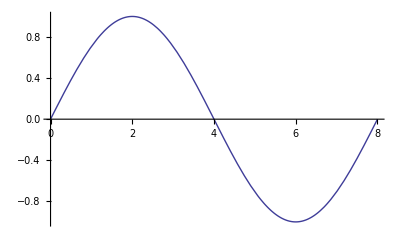

```mathematica
Plot[Sin[(x π)/4],{x,0,8}]
```

```mathematica
Plot[Sin[(x ℼ)/4],{x,0,8}]
```

-Graphics-